# Contouring: Marching Cubes and Dual Contouring

CSE 554 Module 3, Washington University in St. Louis (Fall 2015)

## Introduction

Iso-contours are loci of points having a specific value, called iso-value, in a density function. They are commonly used for data visualization and processing. You will implement some popular countouring algorithms in 2D and 3D.

There are many chances of earning extra credit points in this module. You are required to implement either the primal method (Marching Squares, Marching Cubes) or the dual method (Dual Contouring). Implementing both methods will be extra credit. Also, you can earn more extra credit by implementing some ways of speeding up the contouring algorithm (as we discussed in lecture Contouring II).

## Helpers

In this and subsequent modules, you will be dealing with polylines (in 2D) and meshes (in 3D). A common way of representing them is separately list the geometry (e.g., the X,Y,Z coordinates of vertices) and the connectivity (e.g., what vertices make up a triangle).

For example,  a 2D polyline is a list of two lists {V,E}, where V is a list of vertex coordinates (with X,Y components), and E is a list of edges, each consisting of the indices of its two vertices. Here is a polyline with 3 vertices and 2 edges:

```mathematica
mypoly={{{0,0},{1,2},{2,1}},{{1,2},{2,3}}};
```

Note that the indices of vertices in the edge list {{1,2},{2,3}} starts from 1.

Similarly, a 3D mesh is a list of two lists {V,T}, where V is a list of vertex coordinates (with X,Y,Z components), and T is a list of polygons, each consisting of the indices of its vertices. Here is a mesh with 4 vertices and 2 triangles:

```mathematica
mymesh={{{0,0,0},{1,0,0},{0,1,0},{0,0,1}},{{1,2,3},{1,2,4}}};
```

### Importing images

Sets the default folder to be the folder where this notebook is saved.

```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
```

Constructs a 2D array from input RGB color images by extracting the Red component of each pixel.

```mathematica
PNGtoGray[filename_]:=Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
```

```mathematica
GIFtoGray[filename_]:=255-Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
```

### Showing images

Shows a grayscale image. Note that I added a Transpose and shifted the image by {.5,.5} so that the image will be displayed in the same coordinate system of your iso-curves.

```mathematica
showGrayImage[img_]:=Graphics[Raster[Transpose[(img-Min[img])/(Max[img]-Min[img])],{{.5,.5},Dimensions[img]+.5}],Frame->False];
```

### Showing polylines

This function displays a 2D polyline {V,E} where V is the vertex list and E is the edge list. The function takes in an additional parameter of color (e.g., GrayLevel or RGB).

```mathematica
showCurve[{V_,E_},col_]:=Graphics[{{col,Map[Line[V⟦#⟧]&,E]},Map[Point,V]},Frame->False];
```

For example, let's draw mypoly defined above:

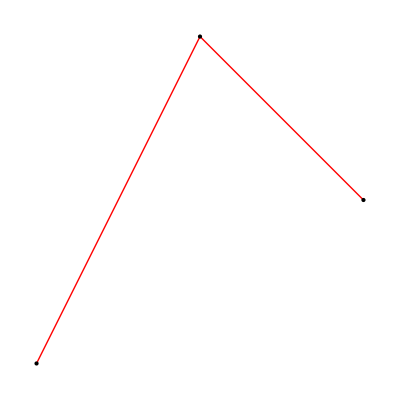

```mathematica
showCurve[mypoly,RGBColor[1,0,0]]
```

Same as above, except the vertices will not be displayed. This is helpful if you have lots of vertices in the curve.

```mathematica
showCurveNoPoints[{V_,E_},col_]:=Graphics[{col,Map[Line[V⟦#⟧]&,E]},Frame->False];
```

### Showing meshes

This function displays a 3D mesh {V,T} where V is the vertex list and T is the triangle list. The function takes in an additional parameter of color (e.g., GrayLevel or RGB).

```mathematica
showSurface[{V_,T_},col_]:=Graphics3D[{col,Map[Polygon[V⟦#⟧]&,T]},RotationAction->Clip,Lighting->"Neutral"];
```

For example, let's draw mymesh defined above:

```mathematica
showSurface[mymesh,RGBColor[1,0,0]]
```

-Graphics3D-

Same as agove, except the polygon edges will not be displayed. This is helpful if you have lots of polygons in the surface.

```mathematica
showSurfaceNoEdges[{V_,T_},col_]:=Graphics3D[{col,EdgeForm[{}],Map[Polygon[V⟦#⟧]&,T]},RotationAction->Clip,Lighting->"Neutral"];
```

## Algorithms

### Computing iso-curves in 2D [6 + 8 pts]

Algorithm 1: [4pts, Extra credit 4 pts] Create a function that takes in a grayscale image and an iso-value, and outputs an iso-curve. Use either Marching Square or Dual Contouring. Implementing a second algorithm gives you extra credit! The iso-curve should be represented as a polyline {V,E}, where V is a list of vertex coordinates (with X,Y components), and E is a list of edges, each consisting of the indices of its two vertices. 

Notes:
1. Assume that the X,Y coordinates of the lower-left corner pixel of the image are {1,1}, and each pixel has size 1.

2. Make sure you don't create the same vertex twice. You can either create an additional array twice as large as the input to store the indices of the vertices after they are created. Alternatively, for better space efficiency (but not as fast), use a hash map to store the index of the created vertex on a grid edge.

3. Take care of the degenerate case where a pixel's value is identical with the iso-value. You can either treat it as above or below the iso-value in your code, just be consistent with your choice for all such pixels.

```mathematica
CalState[i_,j_,img_,iso_]:=Module[
{a,b,c,d},
If[img⟦i,j+1⟧<=iso,a=0,a=1];
If[img⟦i+1,j+1⟧<=iso,b=0,b=1];
If[img⟦i+1,j⟧<=iso,c=0,c=1];
If[img⟦i,j⟧<=iso,d=0,d=1];
Switch[{a,b,c,d},
{0,0,0,0},0,{0,0,0,1},1,{0,0,1,0},2,
{0,0,1,1},3,{0,1,0,0},4,{0,1,0,1},5,
{0,1,1,0},6,{0,1,1,1},7,{1,0,0,0},8,
{1,0,0,1},9,{1,0,1,0},10,{1,0,1,1},11,
{1,1,0,0},12,{1,1,0,1},13,{1,1,1,0},14,
{1,1,1,1},15]]
```

```mathematica
CalState[5,2,imgSyn,0.4];
```

```mathematica
Calt[img_,thr_,i0_,j0_,i1_,j1_]:=Module[
{min,max,t},
min=img⟦i0,j0⟧;
max=img⟦i1,j1⟧;
(*If[min*max≤0,*)
t=(min-thr)/(min-max);
(*,t=min/(min+max)]*)
t]
```

```mathematica
contour2D[img_,iso_]:=Module[
{ni,nj,curve,state,p1,p2,p3,p4,vertex,edge,pos1,pos2,pos3,pos4,e1,e2,t1,t2,t3,t4,result},
{ni,nj}=Dimensions[img];
(*Initiate the output iso-curve list*)
vertex={};
edge={};
Do[
state=CalState[i,j,img,iso];(*Calculate inside/outside state for each vertex*)

If[state==0,Continue[]];

If[state==1,
t1=Calt[img,iso,i,j+1,i,j];(*-Abs[img⟦i,j+1⟧]/(-Abs[img⟦i,j+1⟧]-Abs[img⟦i,j⟧]);*)p1={i,j+1-t1};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i+1,j,i,j];(*-Abs[img⟦i+1,j⟧]/(-Abs[img⟦i+1,j⟧]-Abs[img⟦i,j⟧]);*)
p2={i-t2+1,j};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

e1={pos1,pos2};
If[FreeQ[edge,e1],AppendTo[edge,e1]]
];

If[state==2,
t1=Calt[img,iso,i,j,i+1,j];
(*-Abs[img⟦i,j⟧]/(-Abs[img⟦i,j⟧]-Abs[img⟦i+1,j⟧]);*)p1={i+t1,j};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i+1,j+1,i+1,j];
(*-Abs[img⟦i+1,j+1⟧]/(-Abs[img⟦i+1,j+1⟧]-Abs[img⟦i+1,j⟧]);*)
p2={i+1,j+1-t2};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

e1={pos1,pos2};
If[FreeQ[edge,e1],AppendTo[edge,e1]]
];

If[state==3,
t1=Calt[img,iso,i,j+1,i,j];
(*-Abs[img⟦i,j+1⟧]/(-Abs[img⟦i,j+1⟧]-Abs[img⟦i,j⟧]);*)p1={i,j+1-t1};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i+1,j+1,i+1,j];
(*-Abs[img⟦i+1,j+1⟧]/(-Abs[img⟦i+1,j+1⟧]-Abs[img⟦i+1,j⟧]);*)
p2={i+1,j+1-t2};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

e1={pos1,pos2};
If[FreeQ[edge,e1],AppendTo[edge,e1]]
];

If[state==4,
t1=Calt[img,iso,i,j+1,i+1,j+1];
(*-Abs[img⟦i,j+1⟧]/(-Abs[img⟦i,j+1⟧]-Abs[img⟦i+1,j+1⟧]);*)p1={i+t1,j+1};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i+1,j,i+1,j+1];(*-Abs[img⟦i+1,j⟧]/(-Abs[img⟦i+1,j⟧]-Abs[img⟦i+1,j+1⟧]);*)
p2={i+1,j+t2};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

e1={pos1,pos2};
If[FreeQ[edge,e1],AppendTo[edge,e1]]
];

If[state==5,
t1=Calt[img,iso,i,j+1,i,j];
(*-Abs[img⟦i,j+1⟧]/(-Abs[img⟦i,j+1⟧]-Abs[img⟦i,j⟧]);*)p1={i,j-t1+1};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i,j+1,i+1,j+1];
(*-Abs[img⟦i,j+1⟧]/(-Abs[img⟦i,j+1⟧]-Abs[img⟦i+1,j+1⟧]);*)
p2={i+t2,j+1};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

t3=Calt[img,iso,i+1,j,i,j];
(*-Abs[img⟦i+1,j⟧]/(-Abs[img⟦i+1,j⟧]-Abs[img⟦i,j⟧]);*)
p3={i+1-t3,j};
If[FreeQ[vertex,p3],AppendTo[vertex,p3]];
{{pos3}}=Position[vertex,p3];

t4=Calt[img,iso,i+1,j,i+1,j+1];
(*-Abs[img⟦i+1,j⟧]/(-Abs[img⟦i+1,j⟧]-Abs[img⟦i+1,j+1⟧]);*)
p4={i+1,j+t4};
If[FreeQ[vertex,p4],AppendTo[vertex,p4]];
{{pos4}}=Position[vertex,p4];

e1={pos1,pos2};
e2={pos3,pos4};
If[FreeQ[edge,e1],AppendTo[edge,e1]];
If[FreeQ[edge,e2],AppendTo[edge,e2]];
];

If[state==6,
t1=Calt[img,iso,i,j+1,i+1,j+1];
(*-Abs[img⟦i,j+1⟧]/(-Abs[img⟦i,j+1⟧]-Abs[img⟦i+1,j+1⟧]);*)p1={i+t1,j+1};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i,j,i+1,j];
(*-Abs[img⟦i,j⟧]/(-Abs[img⟦i,j⟧]-Abs[img⟦i+1,j⟧]);*)p2={i+t2,j};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

e1={pos1,pos2};
If[FreeQ[edge,e1],AppendTo[edge,e1]]
];

If[state==7,
t1=Calt[img,iso,i,j+1,i,j];
(*-Abs[img⟦i,j+1⟧]/(-Abs[img⟦i,j+1⟧]-Abs[img⟦i,j⟧]);*)p1={i,j-t1+1};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i,j+1,i+1,j+1];
(*-Abs[img⟦i,j+1⟧]/(-Abs[img⟦i,j+1⟧]-Abs[img⟦i+1,j+1⟧]);*)p2={i+t2,j+1};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

e1={pos1,pos2};
If[FreeQ[edge,e1],AppendTo[edge,e1]]
];

If[state==8,
t1=Calt[img,iso,i,j,i,j+1];
(*-Abs[img⟦i,j⟧]/(-Abs[img⟦i,j⟧]-Abs[img⟦i,j+1⟧]);*)p1={i,j+t1};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i+1,j+1,i,j+1];
(*-Abs[img⟦i+1,j+1⟧]/(-Abs[img⟦i+1,j+1⟧]-Abs[img⟦i,j+1⟧]);*)p2={i-t2+1,j+1};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

e1={pos1,pos2};
If[FreeQ[edge,e1],AppendTo[edge,e1]]
];

If[state==9,
t1=Calt[img,iso,i+1,j+1,i,j+1];
(*-Abs[img⟦i+1,j+1⟧]/(-Abs[img⟦i+1,j+1⟧]-Abs[img⟦i,j+1⟧]);*)p1={i+1-t1,j+1};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i+1,j,i,j];(*-Abs[img⟦i+1,j⟧]/(-Abs[img⟦i+1,j⟧]-Abs[img⟦i,j⟧]);*)
p2={i+1-t2,j};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

e1={pos1,pos2};
If[FreeQ[edge,e1],AppendTo[edge,e1]]
];

If[state==10,
t1=Calt[img,iso,i,j,i,j+1];
(*-Abs[img⟦i,j⟧]/(-Abs[img⟦i,j⟧]-Abs[img⟦i,j+1⟧]);*)p1={i,j+t1};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i,j,i+1,j];
(*-Abs[img⟦i,j⟧]/(-Abs[img⟦i,j⟧]-Abs[img⟦i+1,j⟧]);*)
p2={i+t2,j};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

t3=Calt[img,iso,i+1,j+1,i,j+1];
(*-Abs[img⟦i+1,j+1⟧]/(-Abs[img⟦i+1,j+1⟧]-Abs[img⟦i,j+1⟧]);*)
p3={i+1-t3,j+1};
If[FreeQ[vertex,p3],AppendTo[vertex,p3]];
{{pos3}}=Position[vertex,p3];

t4=Calt[img,iso,i+1,j+1,i+1,j];
(*-Abs[img⟦i+1,j+1⟧]/(-Abs[img⟦i+1,j+1⟧]-Abs[img⟦i+1,j⟧]);*)
p4={i+1,j+1-t4};
If[FreeQ[vertex,p4],AppendTo[vertex,p4]];
{{pos4}}=Position[vertex,p4];

e1={pos1,pos2};
e2={pos3,pos4};
If[FreeQ[edge,e1],AppendTo[edge,e1]];
If[FreeQ[edge,e2],AppendTo[edge,e2]];
];

If[state==11,
t1=Calt[img,iso,i+1,j+1,i,j+1];
(*-Abs[img⟦i+1,j+1⟧]/(-Abs[img⟦i+1,j+1⟧]-Abs[img⟦i,j+1⟧]);*)p1={i+1-t1,j+1};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i+1,j+1,i+1,j];
(*-Abs[img⟦i+1,j+1⟧]/(-Abs[img⟦i+1,j+1⟧]-Abs[img⟦i+1,j⟧]);*)
p2={i+1,j+1-t2};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

e1={pos1,pos2};
If[FreeQ[edge,e1],AppendTo[edge,e1]]
];

If[state==12,
t1=Calt[img,iso,i,j,i,j+1];
(*-Abs[img⟦i,j⟧]/(-Abs[img⟦i,j⟧]-Abs[img⟦i,j+1⟧]);*)p1={i,j+t1};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i+1,j,i+1,j+1];
(*-Abs[img⟦i+1,j⟧]/(-Abs[img⟦i+1,j⟧]-Abs[img⟦i+1,j+1⟧]);*)
p2={i+1,j+t2};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

e1={pos1,pos2};
If[FreeQ[edge,e1],AppendTo[edge,e1]]
];

If[state==13,
t1=Calt[img,iso,i+1,j,i,j];
(*-Abs[img⟦i+1,j⟧]/(-Abs[img⟦i+1,j⟧]-Abs[img⟦i,j⟧]);*)p1={i+1-t1,j};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i+1,j,i+1,j+1];
(*-Abs[img⟦i+1,j⟧]/(-Abs[img⟦i+1,j⟧]-Abs[img⟦i+1,j+1⟧]);*)
p2={i+1,j+t2};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

e1={pos1,pos2};
If[FreeQ[edge,e1],AppendTo[edge,e1]]
];

If[state==14,
t1=Calt[img,iso,i,j,i,j+1];
(*-Abs[img⟦i,j⟧]/(-Abs[img⟦i,j⟧]-Abs[img⟦i,j+1⟧]);*)p1={i(*-1*),j(*-1*)+t1};
If[FreeQ[vertex,p1],AppendTo[vertex,p1]];
{{pos1}}=Position[vertex,p1];

t2=Calt[img,iso,i,j,i+1,j];
(*-Abs[img⟦i,j⟧]/(-Abs[img⟦i,j⟧]-Abs[img⟦i+1,j⟧]);*)
p2={i(*-1*)+t2,j(*-1*)};
If[FreeQ[vertex,p2],AppendTo[vertex,p2]];
{{pos2}}=Position[vertex,p2];

e1={pos1,pos2};
If[FreeQ[edge,e1],AppendTo[edge,e1]]
];

If[state==15,Continue[]];

,{i,ni-1},{j,nj-1}];
result={vertex,edge};
result
]
```

```mathematica
contour2DDual[img_,iso_]:=Module[
{ni,nj,curve,state,p,p1,p2,p3,p4,vertex,edge,pos1,pos2,pos3,pos4,e1,e2,t1,t2,t3,t4,result,index,right,up,rpos,upos,status},
{ni,nj}=Dimensions[img];
(*Initiate the output iso-curve list*)
vertex={};
index={};
edge={};
Do[
state=CalState[i,j,img,iso];(*Calculate inside/outside state for each vertex*)
If[state≠0&&state≠15,AppendTo[index,{i,j}]];
If[state==0,Continue[]];

If[state==1,
t1=Calt[img,iso,i,j+1,i,j];(*-Abs[img⟦i,j+1⟧]/(-Abs[img⟦i,j+1⟧]-Abs[img⟦i,j⟧]);*)
p1={i,j+1-t1};
t2=Calt[img,iso,i+1,j,i,j];
p2={i-t2+1,j};
p={(2*i+1-t2)/2,(2*j+1-t1)/2};
AppendTo[vertex,p];
];

If[state==2,
t1=Calt[img,iso,i,j,i+1,j];
p1={i+t1,j};

t2=Calt[img,iso,i+1,j+1,i+1,j];
p2={i+1,j+1-t2};
p={(2*i+t1+1)/2,(2*j+1-t2)/2};
AppendTo[vertex,p]
];

If[state==3,
t1=Calt[img,iso,i,j+1,i,j];
p1={i,j+1-t1};
t2=Calt[img,iso,i+1,j+1,i+1,j];
p2={i+1,j+1-t2};
p={(2*i+1)/2,j+1-(t1+t2)/2};
AppendTo[vertex,p]
];

If[state==4,
t1=Calt[img,iso,i,j+1,i+1,j+1];
p1={i+t1,j+1};
t2=Calt[img,iso,i+1,j,i+1,j+1];
p2={i+1,j+t2};
p={i+(t1+1)/2,j+(t2+1)/2};
AppendTo[vertex,p]
];

If[state==5,
t1=Calt[img,iso,i,j+1,i,j];
p1={i,j-t1+1};
t2=Calt[img,iso,i,j+1,i+1,j+1];
p2={i+t2,j+1};
t3=Calt[img,iso,i+1,j,i,j];
p3={i+1-t3,j};
t4=Calt[img,iso,i+1,j,i+1,j+1];
p4={i+1,j+t4};
p={i+(t2+1-t3+1)/4,j+(1-t1+1+t4)/4};
AppendTo[vertex,p]
];

If[state==6,
t1=Calt[img,iso,i,j+1,i+1,j+1];
p1={i+t1,j+1};
t2=Calt[img,iso,i,j,i+1,j];
p2={i+t2,j};
p={i+(t1+t2)/2,j+1/2};
AppendTo[vertex,p]
];

If[state==7,
t1=Calt[img,iso,i,j+1,i,j];
p1={i,j-t1+1};
t2=Calt[img,iso,i,j+1,i+1,j+1];
p2={i+t2,j+1};
p={i+t2/2,j+1-t1/2};
AppendTo[vertex,p]
];

If[state==8,
t1=Calt[img,iso,i,j,i,j+1];
p1={i,j+t1};
t2=Calt[img,iso,i+1,j+1,i,j+1];
p2={i-t2+1,j+1};
p={i+(1-t2)/2,j+(t1+1)/2};
AppendTo[vertex,p]
];

If[state==9,
t1=Calt[img,iso,i+1,j+1,i,j+1];
p1={i+1-t1,j+1};
t2=Calt[img,iso,i+1,j,i,j];
p2={i+1-t2,j};
p={i+1-(t1+t2)/2,j+1/2};
AppendTo[vertex,p]
];

If[state==10,
t1=Calt[img,iso,i,j,i,j+1];
p1={i,j+t1};
t2=Calt[img,iso,i,j,i+1,j];
p2={i+t2,j};
t3=Calt[img,iso,i+1,j+1,i,j+1];
p3={i+1-t3,j+1};
t4=Calt[img,iso,i+1,j+1,i+1,j];
p4={i+1,j+1-t4};
p={i+(t2+2-t3)/4,j+(t1+2-t4)/4};
AppendTo[vertex,p]

];

If[state==11,
t1=Calt[img,iso,i+1,j+1,i,j+1];
p1={i+1-t1,j+1};
t2=Calt[img,iso,i+1,j+1,i+1,j];
p2={i+1,j+1-t2};
p={i+1-t1/2,j+1-t2/2};
AppendTo[vertex,p]
];

If[state==12,
t1=Calt[img,iso,i,j,i,j+1];
p1={i,j+t1};
t2=Calt[img,iso,i+1,j,i+1,j+1];
p2={i+1,j+t2};
p={i+1/2,j+(t1+t2)/2};
AppendTo[vertex,p]
];

If[state==13,
t1=Calt[img,iso,i+1,j,i,j];
p1={i+1-t1,j};
t2=Calt[img,iso,i+1,j,i+1,j+1];
p2={i+1,j+t2};
p={i+1-t1/2,j+t2/2};
AppendTo[vertex,p]
];

If[state==14,
t1=Calt[img,iso,i,j,i,j+1];
p1={i(*-1*),j(*-1*)+t1};
t2=Calt[img,iso,i,j,i+1,j];
p2={i(*-1*)+t2,j(*-1*)};
p={i+t2/2,j+t1/2};
AppendTo[vertex,p]
];

If[state==15,Continue[]];
,{i,ni-1},{j,nj-1}];
Do[
{i,j}=index⟦k⟧;
status=CalState[i,j,img,iso];
right={i+1,j};
up={i,j+1};
If[MemberQ[index,right]&&MemberQ[{2,3,4,5,10,11,12,13},status],
{{rpos}}=Position[index,right];
AppendTo[edge,{k,rpos}]];
If[MemberQ[index,up]&&MemberQ[{4,5,6,7,8,9,10},status],
{{upos}}=Position[index,up];
AppendTo[edge,{k,upos}]];
,{k,Length[vertex]}];
result={vertex,edge};
result
]
```

Testing: [2pts] Test your algorithm on the following two examples, a synthetic image created by a function, and a grayscale image loaded from a file. For each example:

1. Use showCurve (in the Helpers) to verify the result of your function with the input image. You can simultaneously show the curve and the original image by the Show command.

2. Make a Manipulate applet that displays the results at varying iso-values (check with Module 0 if you forgot how to use Manipulate).

3. The following showMathematica function displays the result of Mathematica's built-in contouring function (ListContourPlot). Show your result overlaying on Mathematica's (by combining them with Show command).

```mathematica
contourDynamic[img_]:=Manipulate[Show[showGrayImage[img],showCurveNoPoints[contour2D[img,a],RGBColor[0,1,0]],showMathematica[img,a],showCurveNoPoints[contour2DDual[img,a],RGBColor[0,0,1]]],{a,0.0,1.0(*{0.3,0.4,0.5,0.6,0.7,0.8,0.9}*)}]
```

```mathematica
contourDynamic[imgSyn]
```

```mathematica
Show[showGrayImage[imgSyn],showCurveNoPoints[contour2DDual[imgSyn,0.4],RGBColor[1,0,0]],showMathematica[imgSyn,0.4]];
```

```mathematica
Show[showGrayImage[imgSyn],showCurveNoPoints[contour2D[imgSyn,0.4],RGBColor[1,0,0]],showMathematica[imgSyn,0.4]];
```

```mathematica
showMathematica[img_,iso_]:=ListContourPlot[Transpose[img],Contours->{iso},ContourShading->None,ContourStyle->RGBColor[0,0,1],Frame->False,DataRange->Transpose[{{1,1},Dimensions[img]}]];
```

Example 1: A synthetic image (feel free to change the resolution of the image to test your code)

```mathematica
imgSyn=Table[N[Sin[x]Sin[y]],{x,0,2π,2π/30},{y,0,2π,2π/30}];
```

The Mathematica's contour looks like:

```mathematica
Show[showGrayImage[imgSyn],showMathematica[imgSyn,.3]];
```

Example 2: The image in the file "cryo.gif", which is a 2D slice of  3D density volume of a protein imaged by cryo-electron microscopy.

```mathematica
imgCryo=GIFtoGray["cryo.gif"];
```

The Mathematica's contour looks like:

```mathematica
PNGDynamic[img_]:=Manipulate[Show[showGrayImage[img],showCurveNoPoints[contour2D[img,a],RGBColor[0,1,0]],showCurveNoPoints[contour2DDual[img,a],RGBColor[1,0,0]],showMathematica[img,a]],{a,{100,110,120,130,140,150,160,170,180,190,200}}]
```

```mathematica
PNGDynamic[imgCryo]
```

```mathematica
Show[showGrayImage[imgCryo],showCurveNoPoints[contour2D[imgCryo,190],RGBColor[1,0,1]],showMathematica[imgCryo,190]];
```

```mathematica
Show[showGrayImage[imgCryo],showMathematica[imgCryo,120]];
```

Algorithm 2: [Extra credit 4 pts] Design a more efficient algorithm for contouring using either a Quadtree or Interval Tree. Test it out with the examples above (show that the results are identical to those of un-accelerated contouring, and demonstrates the speed-up using Mathematica's Timing function).

### Computing iso-surfaces in 3D [6 + 8 pts]

About Marching Cubes look-up table: The algorithm uses a look-up table to determine how the vertices in a grid cube are connected into triangles. In the data folder, you will find a table I made in Mathematica format ("cycles.txt"). The table contains 256 entries, one for each sign combination of the eight cube corners. Each entry is a list of "cycles" consisting of grid edges of the cube whose vertices should be connected to form a polygon (which may further need to be triangulated).

To use the table, load it first as a Mathematica list:

```mathematica
cycles=Get["cycles.txt"];
```

Let's look at one entry of the table:

```mathematica
Dimensions[cycles[[110]]]
```

{2}

```mathematica
FromDigits[{0,1,0,0,0,1,0,1},2]+1
```

70

```mathematica
Length[cycles⟦123⟧]
cycles[[70]]
```

4

{{{1,2},{2,4},{4,8},{7,8},{5,6}}}

This entry consists of two lists, called cycles. A cycle is a list of grid edges, where each grid edge is represented by indices of its two grid points. Each cycle represents a polygon to be created, whose vertices lie on the grid edges in the cycle. In the case above, both cycles have 3 grid edges, hence they represent two triangles to be built. In general, a cycle may contain more than 3 grid edges, in which case you will need to tessellate the polygon into triangles (e.g., like a fan). The indexing of the eight corners of the cube is shown below:

The index of the entries in the table can be computed from the sign combination at the cube corners in the following way: say all corners are all negative except corners 1 and 7 which are positive. This combination corresponds to the entry with index 10000010 (in base-2) + 1=131 (in decimal), where the binary form has 1 at its 1st and 7th positions. Check out Mathematica's FromDigits function to find out how to create a base-2 number.

To get a better idea of how to use the look-up table, check out the following code that interactively displays the cycles in the table for any given sign combination:

```mathematica
(* locations of 8 cube corners *)
verts=Flatten[Table[{i,j,k},{i,0,1},{j,0,1},{k,0,1}],2];
(* applet *)
Manipulate[signs={v1,v2,v3,v4,v5,v6,v7,v8};
Graphics3D[{
(* draw the cube *)
{Opacity[0],Cuboid[]},
(* draw the cube corners *)
MapThread[{GrayLevel[#2],Cuboid[#1-{.05,.05,.05},#1+{.05,.05,.05}]}&,{verts,signs}],
If[showText,{RGBColor[1,0,0],Table[Text[Style["v"<>ToString[i],20],(verts⟦i⟧-{.5,.5,.5})*1.2+{.5,.5,.5}],{i,8}]},{}],
(* draw the vertices on edges *)
If[showVert,{PointSize[.05],RGBColor[1,.2,.2],Map[Map[Point[Mean[verts⟦#⟧]]&,#]&,cycles⟦FromDigits[signs,2]+1⟧]},{}],
(* draw the triangles *)
If[showPoly,{Opacity[.8],RGBColor[.2,.2,1],Map[Polygon[Map[Mean[verts⟦#⟧]&,#]]&,cycles⟦FromDigits[signs,2]+1⟧]},{}]},
Boxed->False,RotationAction->Clip,Lighting->"Neutral"],
{v1,{0,1}},{v2,{0,1}},{v3,{0,1}},{v4,{0,1}},{v5,{0,1}},{v6,{0,1}},{v7,{0,1}},{v8,{0,1}},{showText,{True,False}},{showPoly,{True,False}},{showVert,{True,False}}]
```

Algorithm 3: [4 pts, Extra credit 4 pts] Create a function that takes in a grayscale volume and an iso-value, and outputs an iso-surface. Use either Marching Cubes or Dual Contouring. Implementing a second algorithm gives you extra credit! The iso-surface should be represented as a triangular mesh {V,T}, where V is a list of vertex coordinates (with X,Y,Z components), and T is a list of triangles, each consisting of the indices of its three vertices.

Notes: Assume that the X,Y,Z coordinates of the lower-left-near corner voxel of the volume are {1,1,1}, and each voxel has size 1. Other notes from the iso-curve algorithm apply here too.

```mathematica
cell={{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}};
```

```mathematica
thres[img_,thr_,x_,y_,z_]:=If[img[[x,y,z]]<thr,0,1]
```

```mathematica
Calt3D[img_,thr_,P1_,P2_]:=Module[
{min,max,t,x1,y1,z1,x2,y2,z2,f1,f2,s},
{x1,y1,z1}=P1;
{x2,y2,z2}=P2;
f1=img⟦x1,y1,z1⟧;
f2=img⟦x2,y2,z2⟧;
If[f1>f2,max=f1;min=f2,max=f2;min=f1];
t=(min-thr)/(min-max);
If[f1>f2,s=0,s=1];
{t,s}]
```

```mathematica
lisss={list}
FromDigits[{},2]+1
```

```mathematica
contour3D[img_,thr_]:=Module[
{nx,ny,nz,v1,v2,v3,v4,v5,v6,v7,v8,sign,trilist,nface,npoint,two,p1,p2,o,P1,P2,t,add,part,if,p,vertex,triangle,result,pos,Pos,tri4,newpos,tri1,tri2,tri3,tri5,tri6},
{nx,ny,nz}=Dimensions[img];
vertex={};
triangle={};
Do[
Do[
Do[
o={x,y,z};
v1=thres[img,thr,x,y,z];
v2=thres[img,thr,x,y,z+1];
v3=thres[img,thr,x,y+1,z];
v4=thres[img,thr,x,y+1,z+1];
v5=thres[img,thr,x+1,y,z];
v6=thres[img,thr,x+1,y,z+1];
v7=thres[img,thr,x+1,y+1,z];
v8=thres[img,thr,x+1,y+1,z+1];

sign={v1,v2,v3,v4,v5,v6,v7,v8};
trilist=cycles⟦FromDigits[sign,2]+1⟧;

If[Dimensions[trilist]=={0},
Continue[],
nface=Length[trilist];
Do[

pos={};
npoint=Length[trilist⟦nf⟧];
Do[
{p1,p2}=trilist⟦nf,np⟧;
P1=o+cell⟦p1⟧;
P2=o+cell⟦p2⟧;
{t,if}=Calt3D[img,thr,P1,P2];
add={0,0,0};
{{part}}=Position[P2-P1,1];
add=ReplacePart[add,part->t];
If[if>0,p=P1+add,p=P2-add];
If[FreeQ[vertex,p],AppendTo[vertex,p]];
{{Pos}}=Position[vertex,p];
AppendTo[pos,Pos]
,{np,npoint}];

If[Length[pos]==3,
AppendTo[triangle,pos]];

If[Length[pos]==4,
tri1={pos⟦1⟧,pos⟦2⟧,pos⟦3⟧};
tri2={pos⟦1⟧,pos⟦3⟧,pos⟦4⟧};
If[FreeQ[triangle,tri1],AppendTo[triangle,tri1]];
If[FreeQ[triangle,tri2],AppendTo[triangle,tri2]]
];

If[Length[pos]==5,
tri1={pos⟦1⟧,pos⟦2⟧,pos⟦3⟧};
tri2={pos⟦1⟧,pos⟦3⟧,pos⟦4⟧};
tri3={pos⟦1⟧,pos⟦4⟧,pos⟦5⟧};
AppendTo[triangle,tri1];
AppendTo[triangle,tri2];
AppendTo[triangle,tri3]
];

If[Length[pos]==6,
tri1={pos⟦1⟧,pos⟦2⟧,pos⟦3⟧};
tri2={pos⟦1⟧,pos⟦3⟧,pos⟦4⟧};
tri3={pos⟦1⟧,pos⟦4⟧,pos⟦5⟧};
tri4={pos⟦1⟧,pos⟦5⟧,pos⟦6⟧};
AppendTo[triangle,tri1];
AppendTo[triangle,tri2];
AppendTo[triangle,tri3];
AppendTo[triangle,tri4]
]
,{nf,nface}]]
,{x,nx-1}],{y,ny-1}],{z,nz-1}];
result={vertex,triangle};
result
]
```

```mathematica
contour3DDual[img_,thr_]:=Module[
{nx,ny,nz,v1,v2,v3,v4,v5,v6,v7,v8,sign,trilist,nface,npoint,two,p1,p2,o,P1,P2,t,add,part,if,p,vertex,triangle,result,pos,Pos,tri4,newpos,tri1,tri2,tri3,tri5,tri6,v,po2pos,po1pos,po3pos,po4pos,po5pos,po6pos,point,index,x0,y0,z0,po1,po2,po3,po4,po5,po6,signlist,signk},
{nx,ny,nz}=Dimensions[img];
index={};
vertex={};
triangle={};
signlist={};
Do[
Do[
Do[
o={x,y,z};
v1=thres[img,thr,x,y,z];
v2=thres[img,thr,x,y,z+1];
v3=thres[img,thr,x,y+1,z];
v4=thres[img,thr,x,y+1,z+1];
v5=thres[img,thr,x+1,y,z];
v6=thres[img,thr,x+1,y,z+1];
v7=thres[img,thr,x+1,y+1,z];
v8=thres[img,thr,x+1,y+1,z+1];

sign={v1,v2,v3,v4,v5,v6,v7,v8};
trilist=cycles⟦FromDigits[sign,2]+1⟧;

If[Dimensions[trilist]=={0},
Continue[],
AppendTo[index,{x,y,z}];
AppendTo[signlist,sign];
nface=Length[trilist];
v={};
Do[
pos={};
npoint=Length[trilist⟦nf⟧];
Do[
{p1,p2}=trilist⟦nf,np⟧;
P1=o+cell⟦p1⟧;
P2=o+cell⟦p2⟧;
{t,if}=Calt3D[img,thr,P1,P2];
add={0,0,0};
{{part}}=Position[P2-P1,1];
add=ReplacePart[add,part->t];
If[if>0,p=P1+add,p=P2-add];
If[FreeQ[v,p],AppendTo[v,p]]
,{np,npoint}]
,{nf,nface}]];
point={0,0,0};
Do[
point=point+v⟦i⟧,{i,Length[v]}];
point=point/Length[v];
AppendTo[vertex,point]
,{x,nx-1}],{y,ny-1}],{z,nz-1}];
Do[
{x0,y0,z0}=index⟦k⟧;
signk=signlist⟦k⟧;

po1={x0+1,y0,z0};
po2={x0+1,y0+1,z0};
po3={x0,y0+1,z0};

po4={x0,y0,z0+1};
po5={x0,y0+1,z0+1};

po6={x0+1,y0,z0+1};

If[MemberQ[index,po1]&&MemberQ[index,po2]&&MemberQ[index,po3]&&((signk⟦7⟧==1&&signk⟦8⟧==0)||(signk⟦7⟧==0&&signk⟦8⟧==1)),
{{po1pos}}=Position[index,po1];
{{po2pos}}=Position[index,po2];
{{po3pos}}=Position[index,po3];AppendTo[triangle,{k,po1pos,po3pos}];
AppendTo[triangle,{po1pos,po2pos,po3pos}]
];

If[MemberQ[index,po3]&&MemberQ[index,po4]&&MemberQ[index,po5]&&((signk⟦4⟧==1&&signk⟦8⟧==0)||(signk⟦4⟧==0&&signk⟦8⟧==1)),
{{po4pos}}=Position[index,po4];
{{po5pos}}=Position[index,po5];
{{po3pos}}=Position[index,po3];
AppendTo[triangle,{po4pos,po5pos,po3pos}];
AppendTo[triangle,{po4pos,k,po3pos}]
];

If[MemberQ[index,po1]&&MemberQ[index,po4]&&MemberQ[index,po6]&&((signk⟦6⟧==1&&signk⟦8⟧==0)||(signk⟦6⟧==0&&signk⟦8⟧==1)),
{{po1pos}}=Position[index,po1];
{{po4pos}}=Position[index,po4];
{{po6pos}}=Position[index,po6];
AppendTo[triangle,{po1pos,po4pos,po6pos}];
AppendTo[triangle,{po1pos,po4pos,k}]
]
,{k,Length[index]}];
result={vertex,triangle};
result
]
```

Testing: [2pts] Test your algorithm on the following synthetic volume created by a function:
1. Use showSurface (in the Helpers) to display the result of your function.

2. Make a Manipulate applet that displays the results at varying iso-values. 

3. The following showMathematica function displays the result of Mathematica's built-in contouring function (ListContourPlot). Show your result overlaying on Mathematica's (by combining them with Show command).

```mathematica
showMathematica3D[img_,iso_]:=ListContourPlot3D[Transpose[img,{3,2,1}],Contours->{iso},ContourStyle->{RGBColor[.5,.5,1]},DataRange->Transpose[{{1,1,1},Dimensions[img]}],Axes->False,RotationAction->Clip,Lighting->"Neutral",PlotRange->All,BoxRatios->Automatic];
```

Example: (feel free to the change the resolution of this image to test out your code)

```mathematica
volSyn=Table[N[Sin[x]Sin[y]Sin[z]],{x,0,2π,2π/15},{y,0,2π,2π/15},{z,0,2π,2π/15}];
```

```mathematica
showSurface[contour3D[volSyn,0],RGBColor[1,0,0]]
```

-Graphics3D-

```mathematica
contour3DDual[volSyn,0.2]
```

{2.58594,2.58594,2.58594}

```mathematica
showSurface[contour3DDual[volSyn,0],RGBColor[1,0,0]]
```

-Graphics3D-

The Mathematica's contour looks like:

```mathematica
showMathematica3D[volSyn,.2]
```

-Graphics3D-

Algorithm 4: [Extra credit 4 pts] Design a more efficient algorithm for iso-surfacing,  using either an Octree or Interval Tree. Test it out with the examples above (show that the results are identical to those of un-accelerated contouring, and demonstrates the speed-up using Mathematica's Timing function).

## Problems

### Contouring a 2D image [2 pts]

Problem 1: [2 pts] The image "humanbrain.png" is a slice of a MRI scan of the human brain. Compute an iso-curve that resembles the following result of Mathematica:

```mathematica
brain=PNGtoGray["humanbrain.png"];
```

```mathematica
Show[showGrayImage[brain],showCurveNoPoints[contour2D[brain,100],RGBColor[1,0,0]],showMathematica[brain,100]]
```

-Graphics-

### Contouring a 3D density volume [4 pts]

Problem 2: [2 pts] The volume "cryo.dat" is a downsampled density volume of a protein imaged with cryo-electron microscopy (you can load it in using Get command, which will return a 3D array). The protein is a folded sequence of amino acids, and visually looks like a winded-up chain. Compute an iso-surface at an approximate iso-value so that the surface has a similar look to the following:

```mathematica
cryo=Get["cryo.dat"];
```

```mathematica
showSurface[contour3D[cryo,0.3],RGBColor[1,0,0]]
```

-Graphics3D-

Problem 3: [2 pts] The volume "foot.dat" is a downsampled CT scan of a human foot (you can load it in using Get command, which will return a 3D array). Different tissues exhibit different levels of intensity in the volume. For example, the skin has a lower density than the bones. Compute iso-surfaces at two iso-values that outline respectively the skin and the bones, as shown below:

```mathematica
foot=Get["foot.dat"];
```

```mathematica
showSurface[contour3D[foot,-900],RGBColor[1,0,0]]
```

-Graphics3D-

```mathematica
-Graphics3D--Graphics3D-
```